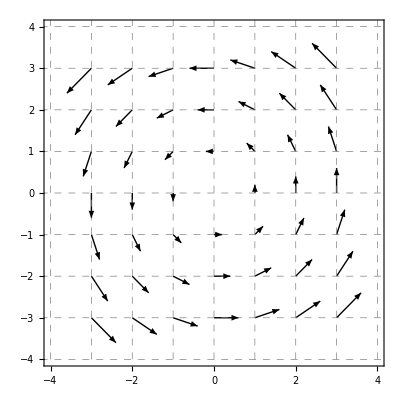

```mathematica
vecField=VectorPlot[{-y,x},{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/rotField.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/rotField.png

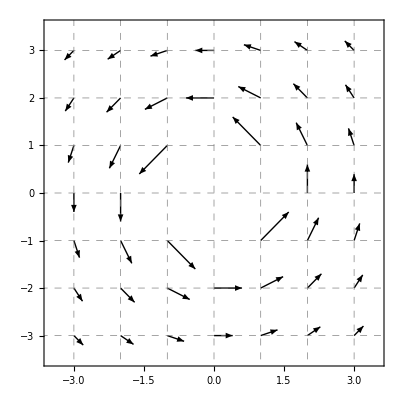

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-y/(x^2+y^2),x/(x^2+y^2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/rotFieldNot.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/rotFieldNot.png

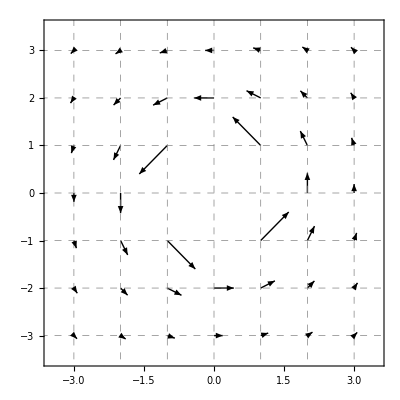

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{-y/(x^2+y^2)^(3/2),x/(x^2+y^2)^(3/2)},{x,-3,3},{y,-3,3},
PlotRange->{{-3.5,3.5},{-3.5,3.5}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/oppoRotField.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/oppoRotField.png

```mathematica
F[x_,y_]={-y/(x^2+y^2)^(3/2),x/(x^2+y^2)^(3/2)}
```

{-y/((x^2+y^2)^(3/2)),x/((x^2+y^2)^(3/2))}

```mathematica
c[x_,y_]=D[F[x,y][[2]],x]-D[F[x,y][[1]],y]
```

-(3 x^2)/((x^2+y^2)^(5/2))-(3 y^2)/((x^2+y^2)^(5/2))+2/((x^2+y^2)^(3/2))

```mathematica
Simplify[-(3 x^2)/((x^2+y^2)^(5/2))-(3 y^2)/((x^2+y^2)^(5/2))+2/((x^2+y^2)^(3/2))]
```

-1/((x^2+y^2)^(3/2))

```mathematica
c[1,0]
```

-1

```mathematica
3
```

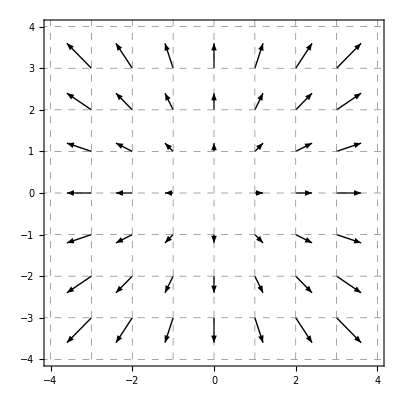

```mathematica
vecField=VectorPlot[{x,y},{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/divField.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/divField.png

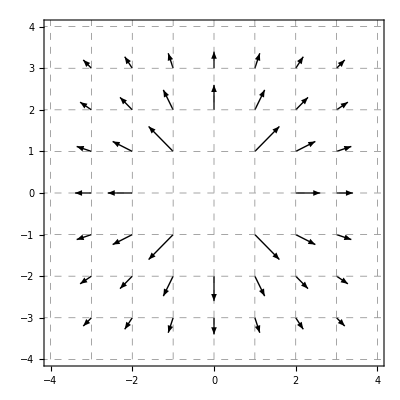

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{x,y}/(Sqrt[x^2+y^2]^2),{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/divFieldZero.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/divFieldZero.png

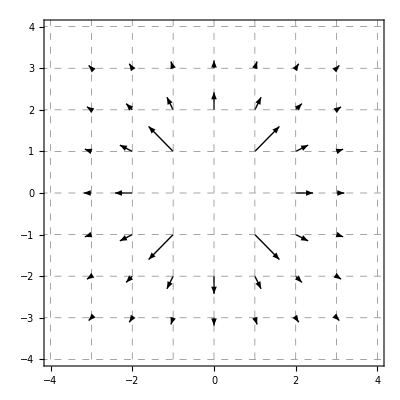

```mathematica
vecField=VectorPlot[Boole[x^2+y^2>1]{x,y}/(Sqrt[x^2+y^2]^3),{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/divFieldNeg.png",vecField]
```

~/teaching/mooculus/calculus3/greensTheorem/divFieldNeg.png

```mathematica
FullSimplify[D[x/(Sqrt[x^2+y^2]^p),x]]
D[y/(Sqrt[x^2+y^2]^p),y]
```

(x^2+y^2)^(-1-p/2) (-(-1+p) x^2+y^2)

-p y^2 (x^2+y^2)^(-1-p/2)+(x^2+y^2)^(-p/2)

```mathematica
Simplify[-p x^2 (x^2+y^2)^(-1-p/2)+(x^2+y^2)^(-p/2)]
```

(x^2+y^2)^(-1-p/2) (-(-1+p) x^2+y^2)

```mathematica
Simplify[-p x^2 (x^2+y^2)^(-1-p/2)-p y^2 (x^2+y^2)^(-1-p/2)+2 (x^2+y^2)^(-p/2)]
```

-(-2+p) (x^2+y^2)^(-p/2)

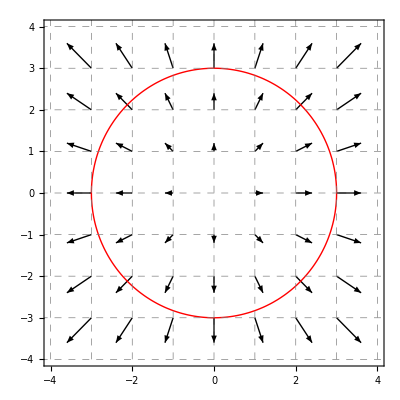

```mathematica
vecField=VectorPlot[{ x ,y},{x,-3,3},{y,-3,3},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}];
circle=ParametricPlot[{3Cos[t],3Sin[t]},{t,0,2Pi},PlotStyle->{Red,Thick}];
circPosDivVecField=Show[vecField,circle]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/circPosDivVecField.png",circPosDivVecField]
```

~/teaching/mooculus/calculus3/greensTheorem/circPosDivVecField.png

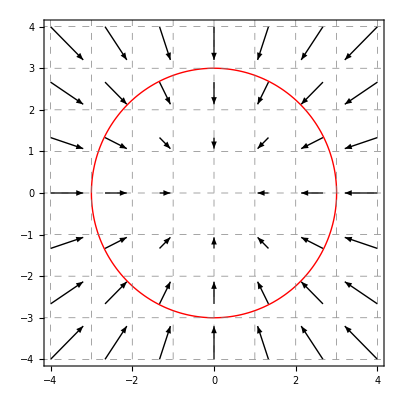

```mathematica
vecField=VectorPlot[{ -x ,-y},{x,-4,4},{y,-4,4},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}];
circle=ParametricPlot[{3Cos[t],3Sin[t]},{t,0,2Pi},PlotStyle->{Red,Thick}];
circNegDivVecField=Show[vecField,circle]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/circNegDivVecField.png",circNegDivVecField]
```

~/teaching/mooculus/calculus3/greensTheorem/circNegDivVecField.png

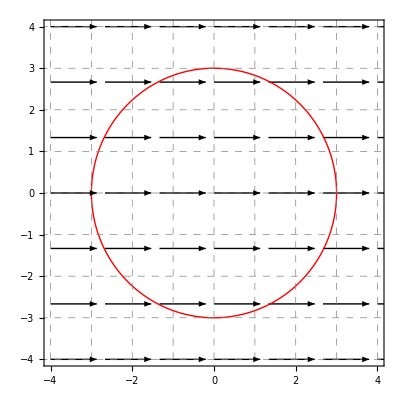

```mathematica
vecField=VectorPlot[{ 1 ,0},{x,-4,4},{y,-4,4},
PlotRange->{{-4,4},{-4,4}},
GridLines->{{-4,-3,-2,-1,0,1,2,3,4},{-4,-3,-2,-1,0,1,2,3,4}},
 VectorPoints->7,
VectorStyle-> Black,
VectorScale->{.1,.6},
GridLinesStyle->Directive[Gray,Dashed]]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}];
circle=ParametricPlot[{3Cos[t],3Sin[t]},{t,0,2Pi},PlotStyle->{Red,Thick}];
circZeroDivVecField=Show[vecField,circle]
```

```mathematica
Export["~/teaching/mooculus/calculus3/greensTheorem/circZeroDivVecField.png",circZeroDivVecField]
```

~/teaching/mooculus/calculus3/greensTheorem/circZeroDivVecField.png